# Lennard-Jones Potential

## Part A

```mathematica
ϵ=.;σ=.;
Vlj[r_]=4ϵ((σ/r)^12-(σ/r)^6) (*Lennard-Jones potential*)

Flj[r_]=24ϵ(2σ^12/r^13-σ^6/r^7)(*Force, which is negative derivative of potential. Could also do -D[Vlj[r],r].*)
```

4 ϵ (-σ^6/r^6+σ^12/r^12)

24 ϵ (-σ^6/r^7+(2 σ^12)/r^13)

```mathematica
ϵ=1;
σ=1;
```

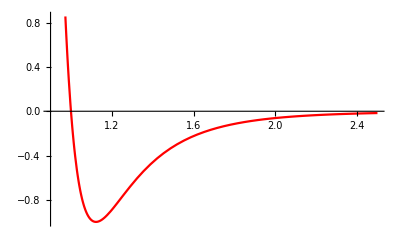

```mathematica
rMin=0.9;
rMax=2.5;

(*Lennard-Jones Potential plot*)
plotV=Plot[Vlj[r],{r,rMin,rMax},PlotStyle->Red]
```

## Part B

```mathematica
NSolve[Flj[r]==0,r]
```

{{r→-1.12246},{r→0.561231-0.972081 ⅈ},{r→0.561231+0.972081 ⅈ},{r→-0.561231-0.972081 ⅈ},{r→-0.561231+0.972081 ⅈ},{r→1.12246}}

The last solution in the array is r = 1.12246. This is the only value that makes sense in context, since it is a real number and positive. Thus, this is the optimal distance (corresponding to minimum potential energy)

## Part C

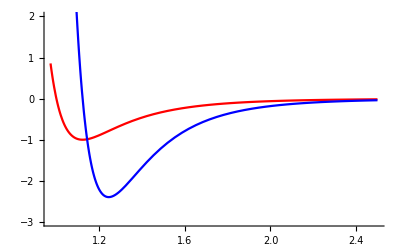

```mathematica
plotF=Plot[Flj[r],{r,rMin,rMax},PlotStyle->Blue];
Show[{plotV,plotF},PlotRange->{-3,2}]
```

## Part D

If the atoms are initially held at a separation of r=1, then the Lennard-Jones potential is:

```mathematica
Vlj[1]
```

0

The equilibrium distance of separation, from part b, is r=1.12246. The Lennard-Jones potential is at a minimum of -1 when r is at this value:

```mathematica
Vlj[1.12246]
```

-1.

Since the equilibrium distance is r=1.2246, where the potential is minimized, atoms that are initially held at r=1 would move apart from each other towards that equilibrium.

# Dynamics

## Part A

```mathematica
x0=2.0;
v0=-0.1;
time=10;
h=0.02;
ϵ=1;
σ=1;
m=1;
nSteps=Round[time/h]
```

500

```mathematica
Clear[x,v,f];
x[0]=x0;
v[0]=v0 ;
f[0]=Flj[x0];
For[n=0,n<=nSteps,n++,
x[n+1]=x[n]+v[n]h+1/2 f[n]/m h^2;
f[n+1]=Flj[x[n+1]];
v[n+1]=v[n]+1/2(f[n]+f[n+1])h/m;
]
```

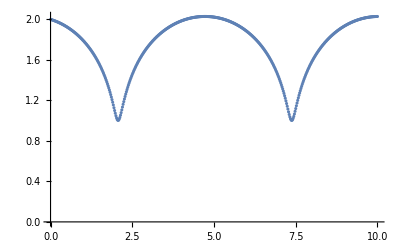

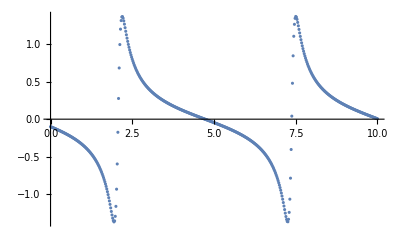

```mathematica
xData=Table[{n h,x[n]},{n,0,nSteps}];
numPlot=ListPlot[xData] (*position graph*)

vData=Table[{n h,v[n]},{n,0,nSteps}];
ListPlot[vData] (*velocity graph*)
```

## Part B

The first graph above is r(t) vs. t, while the second graph is v(t) vs.t (where v is velocity, not potential).

In the r(t) vs. t graph, the shape is pointed at low values of r but broad and smooth at larger values of r. The sharp shape at low values of r close to 1 indicates that the particle has a high velocity and a quick change in velocity to the reverse direction. This happens because at low values of r, the force on the particle is much higher as seen in the steep slope of the force graph in part C, causing a quicker change in position to go towards the equilibrium distance. At greater values of r, the force on the particle becomes very small, causing a much slower change in position. To understand this better, we can plot the force graph again:

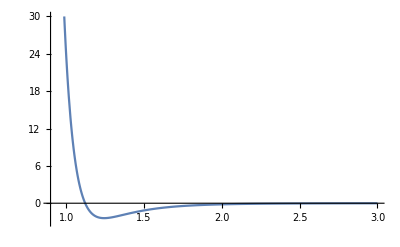

24

```mathematica
Plot[Flj[r],{r,0.9,3}, PlotRange->{-3,30}]
Flj[1]
```

At low values of r, there is a large net force (repulsion+ attraction, with repulsion heavily outweighing the attraction) between the atoms that causes a much greater velocity for them to move apart from each other. As the distance increases (increasing r), the net force becomes very small but is not at zero. There is a small net attractive force still, which causes the atoms to move back to a smaller separation distance but with a much lower velocity.

# Conservation of Energy

## Part A

{-0.0565234,-0.0565237,-0.0565237,-0.0565236,-0.0565233,-0.0565226,-0.0565209,-0.0565161,-0.056498,-0.0563973,-0.0589687,-0.0572253,-0.0564201,-0.0565016,-0.0565169,-0.0565212,-0.0565228,-0.0565234,-0.0565237,-0.0565237,-0.0565237}{0.,-2.44007×10^-7,-3.02845×10^-7,-2.0995×10^-7,8.82099×10^-8,7.90179×10^-7,2.50324×10^-6,7.37594×10^-6,0.0000254621,0.000126155,-0.0024453,-0.000701892,0.000103342,0.0000218531,6.50898×10^-6,2.22043×10^-6,6.78961×10^-7,4.0427×10^-8,-2.28682×10^-7,-3.03696×10^-7,-2.27401×10^-7}0.000556347

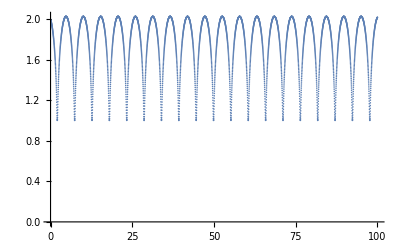

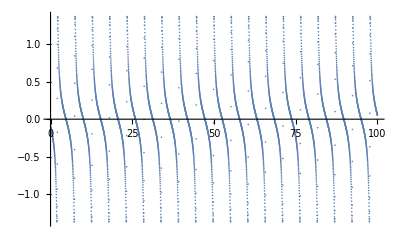

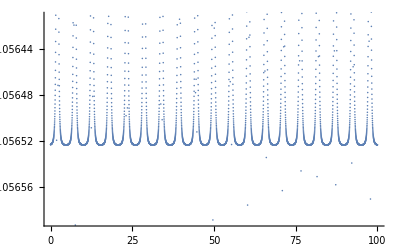

```mathematica
def[h_,v0_]:=(
Clear[x,v,f];
Clear[eOverTime,eErrorOverTime];
eOverTime={};
eErrorOverTime={};

x0=2.0;
time=100;
ϵ=1;
σ=1;
m=1;
eTotal = Vlj[x0]+0.5*m*v0^2;
nSteps=Round[time/h];


x[0]=x0;
v[0]=v0 ;
f[0]=Flj[x0];
e[0]=Vlj[x0]+0.5*m*v[0]^2;
For[n=0,n<=nSteps,n++,
x[n+1]=x[n]+v[n]h+1/2 f[n]/m h^2;
f[n+1]=Flj[x[n+1]];
v[n+1]=v[n]+1/2(f[n]+f[n+1])h/m;
e[n+1]=Vlj[x[n+1]]+0.5*m*(v[n+1])^2;
];

For[i=0,i<=5000,i+=250,
AppendTo[eOverTime,e[i]];
error=e[i]-eTotal;
AppendTo[eErrorOverTime,error];
];
Print[eOverTime,eErrorOverTime,RootMeanSquare[eErrorOverTime]]

)
h=0.02;
v0=-0.1;
def[h,v0]

xData=Table[{n h,x[n]},{n,0,nSteps}];
ListPlot[xData]
vData=Table[{n h,v[n]},{n,0,nSteps}];
ListPlot[vData]
eData=Table[{n h,e[n]},{n,0,nSteps}];
ListPlot[eData]
```

The error in energy is largest when the velocity of the particle changes to move in the opposite direction. This corresponds to the sharp points on the position graph and the asymptotes on the velocity graph. 

However, omitting these points allows us to see that for all of the other points in the simulation, the results for position, velocity, and total energy make sense. The total energy is staying relatively constant throughout the simulation with some fluctuating error, disregarding the asymptotic points for velocity. 

If we consider the higher order error term in the Taylor expansion for the algorithm which indicates the error, the term is highest when the fourth derivative of position and step size are the highest. Since step size can be controlled, redoing the simulation at smaller step sizes is a good way to reduce the size of this higher order term and thus the error of the approximation.

With this current step size of h=0.02, the most error we had for the array of values for total energy (which takes values for every 250 steps up to the total steps of 5000) was about 0.0024453. We can repeat the same method with lower step sizes in Part B and compare the value for highest amount of error from the set of values evaluated.

## Part B

```mathematica
h=0.01;
def[h,v0]
```

{-0.0565234,-0.0564887,-0.0565235,-0.0575117,-0.0565235,-0.0565895,-0.0565235,-0.0565001,-0.0565234,-0.0565184,-0.0565232,-0.0565219,-0.0565228,-0.0565229,-0.0565216,-0.0565233,-0.0565169,-0.0565234,-0.0564906,-0.0565235,-0.0572826}{0.,0.0000347776,-6.10859×10^-8,-0.000988284,-7.56966×10^-8,-0.0000660275,-5.21684×10^-8,0.0000232946,2.31289×10^-8,5.03332×10^-6,2.00698×10^-7,1.5164×10^-6,6.35548×10^-7,5.16829×10^-7,1.87945×10^-6,1.53956×10^-7,6.53915×10^-6,3.08196×10^-9,0.0000327988,-5.99381×10^-8,-0.000759113}0.000272573

The highest error in the set of values that was evaluated with step size of 0.01, was about .00076. The error in approximation for total energy slowly decreased with the more time that passed, but suddenly increased for the last value in the array evaluated at steps=5000 or t=50. If we use a lower step size than this, it might minimize the error further to a more acceptable level.

```mathematica
h=0.005;
def[h,v0]
```

{-0.0565234,-0.0565222,-0.0565147,-0.0565234,-0.0565235,-0.0565231,-0.0567729,-0.0565233,-0.0565235,-0.0565233,-0.0565396,-0.056523,-0.0565235,-0.0565234,-0.0565176,-0.0565218,-0.0565234,-0.0565234,-0.0565222,-0.0565149,-0.0565234}{0.,1.23154×10^-6,8.70429×10^-6,5.12964×10^-8,-1.52768×10^-8,3.72126×10^-7,-0.00024944,1.61881×10^-7,-1.89232×10^-8,1.26786×10^-7,-0.0000161228,4.79575×10^-7,-1.30224×10^-8,3.74886×10^-8,5.80602×10^-6,1.67809×10^-6,5.84905×10^-9,3.26341×10^-10,1.25442×10^-6,8.48927×10^-6,5.03708×10^-8}0.0000546277

The highest error in this set of values is about 0.00025. This error was also relatively early on in terms of the time. The error quickly stabilizes to at least 10^-6 order for most of the set. There is one other point that gave a somewhat high error of 0.000016, but even after that the error quickly returned to a low value. This shows that there is still some slight error inherent in the approximation that reappears, but the fact that the error quickly recovers to a very low value with very few data points that have significant error shows that the simulation is now mostly accurate and h=0.005 is most likely a reasonable step size to minimize error.

## Part C

Now we will run the simulation again but with a system that has a higher total energy. This will be done by having a higher initial velocity. We will keep the step size at 0.02 while using progressively larger initial velocities.

```mathematica
h=0.005;
```

```mathematica
v0=-0.1;
def[h,v0]
```

{-0.0565234,-0.0565222,-0.0565147,-0.0565234,-0.0565235,-0.0565231,-0.0567729,-0.0565233,-0.0565235,-0.0565233,-0.0565396,-0.056523,-0.0565235,-0.0565234,-0.0565176,-0.0565218,-0.0565234,-0.0565234,-0.0565222,-0.0565149,-0.0565234}{0.,1.23154×10^-6,8.70429×10^-6,5.12964×10^-8,-1.52768×10^-8,3.72126×10^-7,-0.00024944,1.61881×10^-7,-1.89232×10^-8,1.26786×10^-7,-0.0000161228,4.79575×10^-7,-1.30224×10^-8,3.74886×10^-8,5.80602×10^-6,1.67809×10^-6,5.84905×10^-9,3.26341×10^-10,1.25442×10^-6,8.48927×10^-6,5.03708×10^-8}0.0000546277

```mathematica
v0=-0.2;
def[h,v0]
```

{-0.0415234,-0.041518,-0.0415217,-0.0415235,-0.0415235,-0.0415235,-0.0415219,-0.0415168,-0.0415234,-0.0415235,-0.0415235,-0.0415229,-0.0415138,-0.0415234,-0.0415235,-0.0415235,-0.0415232,-0.0414796,-0.0415232,-0.0415235,-0.0415235}{0.,5.39193×10^-6,1.77061×10^-6,-3.00722×10^-8,-7.20204×10^-8,-3.37464×10^-8,1.49637×10^-6,6.64436×10^-6,6.9385×10^-9,-7.08505×10^-8,-5.21659×10^-8,5.17149×10^-7,9.61466×10^-6,8.03816×10^-8,-6.73562×10^-8,-6.25888×10^-8,1.90709×10^-7,0.0000438639,2.42231×10^-7,-6.0632×10^-8,-6.84251×10^-8}9.98922×10^-6

```mathematica
v0=-0.5;
def[h,v0]
```

{0.0634766,0.0640641,0.0634765,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762,0.0634762}{0.,0.000587554,-1.68932×10^-8,-3.24938×10^-7,-3.49389×10^-7,-3.54188×10^-7,-3.55535×10^-7,-3.55996×10^-7,-3.56175×10^-7,-3.56252×10^-7,-3.56287×10^-7,-3.56305×10^-7,-3.56314×10^-7,-3.56319×10^-7,-3.56322×10^-7,-3.56324×10^-7,-3.56325×10^-7,-3.56325×10^-7,-3.56326×10^-7,-3.56326×10^-7,-3.56326×10^-7}0.000128215

```mathematica
v0=-1;
def[h,v0]
```

{0.438477,0.438487,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475,0.438475}{0.,0.0000106482,-1.2388×10^-6,-1.31722×10^-6,-1.32157×10^-6,-1.32207×10^-6,-1.32216×10^-6,-1.32219×10^-6,-1.32219×10^-6,-1.32219×10^-6,-1.32219×10^-6,-1.32219×10^-6,-1.32219×10^-6,-1.32219×10^-6,-1.3222×10^-6,-1.3222×10^-6,-1.3222×10^-6,-1.3222×10^-6,-1.3222×10^-6,-1.3222×10^-6,-1.3222×10^-6}2.64008×10^-6

```mathematica
v0=-2;
def[h,v0]
```

{1.93848,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847,1.93847}{0.,-4.19157×10^-6,-5.18167×10^-6,-5.18542×10^-6,-5.18556×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6,-5.18557×10^-6}5.01636×10^-6

```mathematica
v0=-10;
def[h,v0]
```

{49.9385,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384,49.9384}{0.,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477,-0.0000891477}0.0000869993

Since the step size of h=0.005 is so small, it is difficult to know for certain whether the error is increasing with larger values for the initial velocity. Thus, it was necessary to increase the velocity significantly to integer values in order to prove that error was increasing. This is a good sign as it indicates that our step size is small enough to reduce error even at reasonably high velocities.

However, this part still proves that error increases with increasing total energy, requiring a smaller step size at a point to reduce error. This is possibly because with increased energy due to increased initial velocity, the margin of error in the velocity verlet algorithm to obtain the next values for velocity increases. A higher starting velocity for the algorithm means every successive velocity which depends on the previous will have a higher amount of error compared to the amount of error that was present for these velocity approximations with a lower starting velocity. As a result, the energy calculations will also have a higher amount of error as they are calculated using the velocities.

## Bonus

```mathematica
RMSEarray={};
def[h_,v0_]:=(
Clear[x,v,f];
Clear[eOverTime,eErrorOverTime];
eOverTime={};
eErrorOverTime={};


x0=2.0;
time=100;
ϵ=1;
σ=1;
m=1;
eTotal = Vlj[x0]+0.5*m*v0^2;
nSteps=Round[time/h];


x[0]=x0;
v[0]=v0 ;
f[0]=Flj[x0];
e[0]=Vlj[x0]+0.5*m*v[0]^2;
For[n=0,n<=nSteps,n++,
x[n+1]=x[n]+v[n]h+1/2 f[n]/m h^2;
f[n+1]=Flj[x[n+1]];
v[n+1]=v[n]+1/2(f[n]+f[n+1])h/m;
e[n+1]=Vlj[x[n+1]]+0.5*m*(v[n+1])^2;
];

For[i=0,i<=5000,i+=250,
AppendTo[eOverTime,e[i]];
error=e[i]-eTotal;
AppendTo[eErrorOverTime,error];
];
RMSEarray=AppendTo[RMSEarray,RootMeanSquare[eErrorOverTime]];

)
```

```mathematica
v0=-0.1;
RMSEarray={};
def[0.0009,v0];
def[0.0008,v0];
def[0.0007,v0];
def[0.0006,v0];
def[0.0004,v0];
Print[RMSEarray]
hData={0.0009,0.0008,0.0007,0.0006,0.0004}
```

{1.8162×10^-6,3.05093×10^-6,5.75535×10^-7,8.36445×10^-7,7.21363×10^-7}

{0.0009,0.0008,0.0007,0.0006,0.0004}

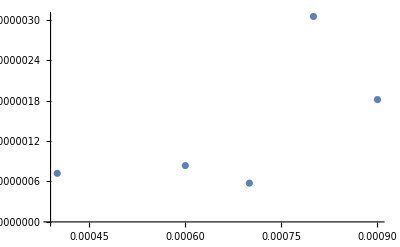

```mathematica
ListPlot[Transpose[{hData,RMSEarray}]]
```

There doesn’t seem to be a linear relationship here. There are a few bugs since running the def method for some step sizes returned the energy and error arrays of the previous run. If the method’s loop didn’t work, the arrays should’ve at least been empty rather than having the previous values so I don’t know what’s happening. The RMSE also seems to be pretty inconsistent.